# Lab 01

## ELLIOTTCABLE, IIT

Problems

The first four problems below are fairly routine, but they all contain ideas about limits that you need to know for our course.

## Problem 1

1.	The function f(x)=(sin(x))/x is called the “sinc” function.

```mathematica
Clear[sinc];sinc[x_]:=Sin[x]/x
```

a)	Create a table of values to find lim_(x→ 0) (sin(x))/x

```mathematica
Table[sinc[1/n],{n,1,10}] // N
```

{0.841471,0.958851,0.981584,0.989616,0.993347,0.995377,0.996602,0.997398,0.997944,0.998334}

b)	Plot f(x) on the interval [-6,6]

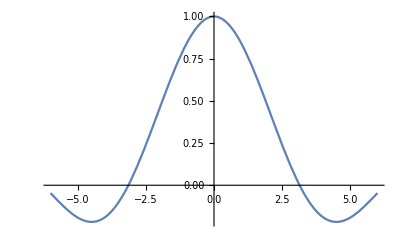

```mathematica
Plot[sinc[x], {x, -6, 6}]
```

c)	Is f(x) as defined a continuous function? What is f(0)?

It is non-continuous: f(0) is indeterminate.

```mathematica
sinc[x] /. x -> 0
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

d) 	Compute  lim_(x→ 0) (sin(x))/x using Mathematica

```mathematica
Limit[sinc[x],x->0]
```

e)	How would you define f(0) in order to remove the discontinuity?

```mathematica
Piecewise[{{sinc[x],x≠0},{1,x==0}}]
```

Piecewise[{{Sin[x]/x, x≠0}, {1, x==0}, {0, True}}]

f)	Are there any algebraic calculations you can do to find lim_(x→ 0) (sin(x))/x that don't already involve further ideas from 		calculus?  If yes, do them using Mathematica!

Nope!

## Problem 2

2.		Consider the function f(x)=(1-cos(x))/x

```mathematica
Clear[prob2];prob2[x_]:=(1-Cos[x])/x
```

a)	Create a table of values to find lim_(x→ 0) (1-cos(x))/x

```mathematica
Table[prob2[1/n],{n,1,10}] // N
```

{0.459698,0.244835,0.165129,0.12435,0.0996671,0.0831406,0.0713072,0.0624187,0.0554984,0.0499583}

b)	Plot f(x) on the interval [-6,6]

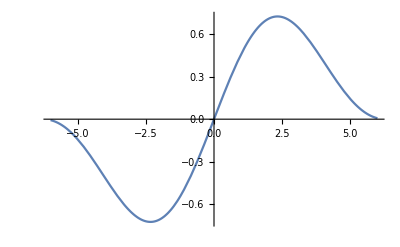

```mathematica
Plot[prob2[x], {x, -6, 6}]
```

c)	Is f(x) as defined a continuous function? What is f(0)?

```mathematica
It is non-continuous: f(0) is indeterminate.
```

```mathematica
prob2[x] /. x -> 0
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

d) 	Compute  lim_(x→ 0) (1-cos(x))/x using Mathematica
	e)	How would you define f(0) in order to remove the discontinuity?
f)	Are there any algebraic calculations you can do to find lim_(x→ 0) (1-cos(x))/x that don't already involve further ideas from 		calculus?  If yes, do them using Mathematica!

## Problem 3

3.	Consider the function f(x)=(1+x)^(1/x)  
	a)	Create a table of values to find lim_(x→ 0) (1+x)^(1/x)
	b)	Plot f(x) on the interval [0,6]
	c)	Is f(x) as defined a continuous function? What is f(0)?
	d) 	Compute  lim_(x→ 0) (1+x)^(1/x) using Mathematica
	e)	How would you define f(0) in order to remove the discontinuity?
	f)	Are there any algebraic calculations you can do to find lim_(x→ 0) (1+x)^(1/x) that don’t already involve further ideas 			from calculus?  If yes, do them using Mathematica!

## Problem 4

4.	Consider the function f(x)=((2+x)^3-8)/x

```mathematica
Clear[prob4];prob4[x_]:=((2+x)^3-8)/x
```

a)	Create a table of values to find lim_(x→ 0) ((2+x)^3-8)/x

```mathematica
Table[prob4[1/n], {n, 1, 100}] // N
```

{19.,15.25,14.1111,13.5625,13.24,13.0278,12.8776,12.7656,12.679,12.61,12.5537,12.5069,12.4675,12.4337,12.4044,12.3789,12.3564,12.3364,12.3186,12.3025,12.288,12.2748,12.2628,12.2517,12.2416,12.2322,12.2236,12.2156,12.2081,12.2011,12.1946,12.1885,12.1827,12.1773,12.1722,12.1674,12.1629,12.1586,12.1545,12.1506,12.1469,12.1434,12.1401,12.1369,12.1338,12.1309,12.1281,12.1254,12.1229,12.1204,12.118,12.1158,12.1136,12.1115,12.1094,12.1075,12.1056,12.1037,12.102,12.1003,12.0986,12.097,12.0955,12.094,12.0925,12.0911,12.0898,12.0885,12.0872,12.0859,12.0847,12.0835,12.0824,12.0813,12.0802,12.0791,12.0781,12.0771,12.0761,12.0752,12.0742,12.0733,12.0724,12.0716,12.0707,12.0699,12.0691,12.0683,12.0675,12.0668,12.0661,12.0653,12.0646,12.0639,12.0633,12.0626,12.062,12.0613,12.0607,12.0601}

b)	Plot f(x) on the interval [0,6]

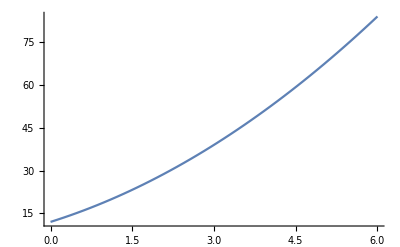

```mathematica
Plot[prob4[x], {x, 0, 6}]
```

```mathematica
Simplify[prob4[x]]
```

12+6 x+x^2

c)	Is f(x) as defined a continuous function? What is f(0)?

d) 	Compute  lim_(x→ 0) ((2+x)^3-8)/x using Mathematica

e)	How would you define f(0) in order to remove the discontinuity?
	f)	Are there any algebraic calculations you can do to find lim_(x→ 0) ((2+x)^3-8)/x that don't already involve further ideas from 		calculus? If yes, do them using Mathematica!

## Problems 5 & 6

5.	Verify that the the slope of the tangent line to the function f(x)=-x^3 + x^2+ 12x- 3 from the Manipulate above at x=0, 	is the same as what you would get if you used the D operator. Now do the same for x=1, 2, and 3.

```mathematica
f[x_]=-(x^3) + (x^2) + (12*x) - 3;
  
(* define a function of x here *)
xmin = -6;                              (* function max and min x values set here *)
xmax = 6;

astart = -3;      (* point of tangency starting point value *)
amin = -4.3;      (* point of tangency minimum value *)
amax= 5;          (* point of tangency maximum value *)

hstart = -1;      (* Secant line intersection starting point *)
hmin = -1.3;      (* Secant line intersection minimum value *)
hmax = 8.5;       (* Secant line intersection maximum value *)
```

```mathematica
Manipulate[
   If[h==0,h=.001];Grid[{{Plot[{f[x],If[True,f[a]+(D[f[t],t]/.t->a)*(x-a)], f[a]+((f[a+h]-f[a])/h)*(x-a)} , {x,xmin,xmax}, PlotStyle->{{Thickness[.005],Black},{Thickness[.004],Blue}, {Thickness[.004],Red}},PlotRange->{15*xmin,(8*xmax) + 2}, ImageSize->{475,325},PlotLabel ->Style[Row[{Style["f(x)",Italic]," = ",ToString[- x^3+ x^2+ 12 x - 3,TraditionalForm]}],20],AxesLabel-> {Style["x",16,Italic],Style["y",16,Italic]},Prolog->{{PointSize[.02],If[True,Blue,Red], Point[{a,f[a]}]},{PointSize[.02],Red, Point[{a+h,f[a+h]}]}}]},{Row[{If[True,Style[Text["tangent slope = "<>ToString[D[f[t],t]/.t->a]], Blue, 20]],Style[Text["secant slope =  "<>ToString[(f[a+h]-f[a])/h]], Red, 20]},"    "]}}], 
{{a, astart,"x_0"},amin,amax},
 {{h,hstart,"h"}, hmin,hmax},
(*{{tl,False,"tangent line"},{True,False}},*)
TrackedSymbols->{a,h}, SaveDefinitions->True]
```

6.	Use the Manipulate above to try and estimate where the slope of the tangent line is equal to zero, then figure out where 	this happens using the commands built into 	Mathematica and compare your estimate to the value you found. We will be spending a great deal of time doing this sort of calculation. You will need to use the N function to get some 		decimals at some point.

```mathematica
D[-(x^3) + (x^2) + (12*x) - 3, x]
```

```mathematica
Solve[12+2 x-3 x^2 == 0, x] // N
```

{{x→-1.69425},{x→2.36092}}